```mathematica
(* This removes the majority of the data that we're not interested in for Faraday rotation purposes*)
stepColumn=3;
intensityColumn=4;
dataStartRow=16;
StripRawData[data_]:=Take[data,{dataStartRow,-1},{intensityColumn,intensityColumn}];

(* Sets the Base directory, changing which files are easiest to acces. *)
dropBoxOn=FileNameJoin[{"Dropbox","00School","research"}];
labComp=FileNameJoin[{"C:","Users","karl",dropBoxOn}];(* Lab computer is Windows, so needs "C:" at beginning"  *)
homeComp=FileNameJoin[{"/","home","karl",dropBoxOn}]; (* Home coputer is Linux, so needs "/" at beginning *)
(* The folder that contains the different data runs to analyze, this folder contains subfolders with 
individual runs.*)
dataFolder=FileNameJoin[{labComp}]
SetDirectory[dataFolder];
(* Make a list of directories to easily select the folder you would like to work with.*)
directories=Select[FileNames["*","",1],DirectoryQ];
For[i=1,i<=Length[directories],i++,
Print[i -> directories[[i]]];]
```

C:\Users\karl\Dropbox\00School\research

1→05-19-17_BetterLaser

2→3_15_17_AimingFor5e12

3→4-18-17

4→4-22-17

5→4-25-17_ProbePolarizationDriftOpenChamber

6→4-30-17_laserReport

7→5-17-17_DirtyGunRun

8→data

9→Data Before 4-1-17

10→firstRun2017

11→GPIB Project

12→labBook

13→legacy

14→machineShopOrders

15→mathematicaRb

16→New folder

17→operationManuals

18→papers

19→polarization_4-18-17

20→polarization_4-4-17

21→polarization_4-6-17

22→probeLaserPower

23→pumpLaserFindingCircular_3-29_17

24→RbControlPiPrograms

25→rbsim

26→requisitions

27→reverseEngineeringWavemeter

28→temp

29→wavemeterNoRb

30→wavemeterReliability_3-30-17

31→wmReliability_4-7-17

```mathematica
(* set rootFolder to the folder name containing the desired Files *)
rootFolder=FileNameJoin[{dataFolder,directories[[1]]}];
SetDirectory[rootFolder];
(* Obtain the filenames of the rotation data and print them out.*)
scanFiles=FileNames["FDayScan"~~RegularExpression[".{17,17}"]~~".dat"];
For[i=1,i<=Length[scanFiles],i++,
Print[i -> scanFiles[[i]]];]
```

1→FDayScan2017-05-19_000023.dat

2→FDayScan2017-05-19_000126.dat

3→FDayScan2017-05-19_000245.dat

4→FDayScan2017-05-19_000409.dat

5→FDayScan2017-05-19_000515.dat

6→FDayScan2017-05-19_000600.dat

7→FDayScan2017-05-19_000725.dat

8→FDayScan2017-05-19_000835.dat

9→FDayScan2017-05-19_000932.dat

10→FDayScan2017-05-19_001156.dat

11→FDayScan2017-05-19_133736.dat

12→FDayScan2017-05-19_133905.dat

13→FDayScan2017-05-19_141808.dat

14→FDayScan2017-05-19_142628.dat

15→FDayScan2017-05-19_143446.dat

16→FDayScan2017-05-19_144433.dat

17→FDayScan2017-05-19_145326.dat

18→FDayScan2017-05-19_150145.dat

19→FDayScan2017-05-19_153206.dat

20→FDayScan2017-05-19_154008.dat

21→FDayScan2017-05-19_154009.dat

22→FDayScan2017-05-19_154027.dat

23→FDayScan2017-05-19_154939.dat

24→FDayScan2017-05-19_155757.dat

25→FDayScan2017-05-19_161230.dat

26→FDayScan2017-05-19_162055.dat

27→FDayScan2017-05-19_162917.dat

28→FDayScan2017-05-19_170542.dat

29→FDayScan2017-05-19_171409.dat

30→FDayScan2017-05-19_172325.dat

31→FDayScan2017-05-19_174444.dat

32→FDayScan2017-05-19_175316.dat

33→FDayScan2017-05-19_180159.dat

34→FDayScan2017-05-19_181404.dat

35→FDayScan2017-05-19_182321.dat

36→FDayScan2017-05-19_183134.dat

37→FDayScan2017-05-19_191227.dat

38→FDayScan2017-05-19_191331.dat

39→FDayScan2017-05-19_192201.dat

40→FDayScan2017-05-19_193028.dat

41→FDayScan2017-05-19_194106.dat

42→FDayScan2017-05-19_194928.dat

43→FDayScan2017-05-19_195749.dat

```mathematica
fileNumber=34;
rawRotationDataFile=Import[FileNameJoin[{rootFolder,scanFiles[[fileNumber]]}],"tsv"];
rawRotationData=Transpose[StripRawData[rawRotationDataFile]]
```

{{-0.142358,-0.086292,-0.048737,-0.024388,-0.010725,-0.012175,-0.028243,-0.054958,-0.097742,-0.160563,-0.227849,-0.291776,-0.332499,-0.371847,-0.407341,-0.428256,-0.456155,-0.454934,-0.446576,-0.424249,-0.395815,-0.366352,-0.318835,-0.263076,-0.205445,-0.13732,-0.08446,-0.048203,-0.023472,-0.010343,-0.012442,-0.028128,-0.057134,-0.102207,-0.161288,-0.218078,-0.27048,-0.31353,-0.352765,-0.395129,-0.427722,-0.446232,-0.45024,-0.440469,-0.413753,-0.384099,-0.352039,-0.317042,-0.270709,-0.2093,-0.145067,-0.087018,-0.049424,-0.024884,-0.01103,-0.011831,-0.026601,-0.052974,-0.094803,-0.153311,-0.221322,-0.286357,-0.337384,-0.373794,-0.407074,-0.43131,-0.451652,-0.459132,-0.44711,-0.426882,-0.398945,-0.365016,-0.323911,-0.271052,-0.209186,-0.142205,-0.088735,-0.051256,-0.02538,-0.010686,-0.011831,-0.026449,-0.055187,-0.100223,-0.157967,-0.211323,-0.265556,-0.311126,-0.350284,-0.390587,-0.4236,-0.443904,-0.457033,-0.444057,-0.418486,-0.385587,-0.357116,-0.321316,-0.275594,-0.21762,-0.14896,-0.0903,-0.052783,-0.026792,-0.011679,-0.011373,-0.025304,-0.0516,-0.093239,-0.154075,-0.221284,-0.283952,-0.329942,-0.368947,-0.403296,-0.435928,-0.459628,-0.45856,-0.450507,-0.428409,-0.401197,-0.369558,-0.33143,-0.276357,-0.211934,-0.144877,-0.08904,-0.051791,-0.026372,-0.011144,-0.011297,-0.025037,-0.053203,-0.099383,-0.154571,-0.209873,-0.263915,-0.305783,-0.346429,-0.391121,-0.424669,-0.440698,-0.454133,-0.437988,-0.41986,-0.389633,-0.35807,-0.32498,-0.284525,-0.218918,-0.082171,-0.090185,-0.052859,-0.026716,-0.011412,-0.011106,-0.024846,-0.050493,-0.091254,-0.149762,-0.213689,-0.276892,-0.327423,-0.361238,-0.398792,-0.422417,-0.451423,-0.455316,-0.452491,-0.427989,-0.40009,-0.36597,-0.3254,-0.278876,-0.215979,-0.147434,-0.091788,-0.053737,-0.026525,-0.011297,-0.011183,-0.024426,-0.053203,-0.098353,-0.15312,-0.206858,-0.256168,-0.306508,-0.338109,-0.387992,-0.419326,-0.440851,-0.455507,-0.446003,-0.415776,-0.397609,-0.364062,-0.326698,-0.286586,-0.222734,-0.152701,-0.093086,-0.054424,-0.027975,-0.01206,-0.010839,-0.02454,-0.050417,-0.091597,-0.149418,-0.219147,-0.27838,-0.326278,-0.367802,-0.40383,-0.432378,-0.450431,-0.461842,-0.453675,-0.433332,-0.396617,-0.371466,-0.33414,-0.28109,-0.213918,-0.145487,-0.090834,-0.053775,-0.027441,-0.011526,-0.010954,-0.024273,-0.051753,-0.096559,-0.151899,-0.211285,-0.259755,-0.305592,-0.351963,-0.39593,-0.428104,-0.449476,-0.454438,-0.448026,-0.426844,-0.394136,-0.363985,-0.325743,-0.283532,-0.222849,-0.08427,-0.092284,-0.053623,-0.027517,-0.011793,-0.010801,-0.024579,-0.050569,-0.09133,-0.148884,-0.216819,-0.279639,-0.329636,-0.365436,-0.400357,-0.428409,-0.446614,-0.459857,-0.448102,-0.42963,-0.406349,-0.37139,-0.325591,-0.278647,-0.215636,-0.149151,-0.093277,-0.054615,-0.027785,-0.011526,-0.010954,-0.024464,-0.05202,-0.097742,-0.152319,-0.207468,-0.259831,-0.306622,-0.345246,-0.388793,-0.418715,-0.438904,-0.453255,-0.443103,-0.42047,-0.388106,-0.358337,-0.325247,-0.283074,-0.222391,-0.153235,-0.092819,-0.054119,-0.027823,-0.011984,-0.010457,-0.02435,-0.049653,-0.090949,-0.146098,-0.217277,-0.279143,-0.326927,-0.367344,-0.399708,-0.429477,-0.446309,-0.454476,-0.44795,-0.434019,-0.40654,-0.37242,-0.332537,-0.279945,-0.21575,-0.146098,-0.090758,-0.054004,-0.028166,-0.011717,-0.010763,-0.024159,-0.051066,-0.095757,-0.15125,-0.207087,-0.259144,-0.299944,-0.345093,-0.389862,-0.424287,-0.446423,-0.455659,-0.440927,-0.422913,-0.390205,-0.35765,-0.327881,-0.284296,-0.21701,-0.152624,-0.092895,-0.053546,-0.027556,-0.011717,-0.010954,-0.024464,-0.049195,-0.089308,-0.147396,-0.215483,-0.278609,-0.331048,-0.366924,-0.401884,-0.434783,-0.45024,-0.461422,-0.448026,-0.426234,-0.398029,-0.376809,-0.332155,-0.279601,-0.21388,-0.148044,-0.093391,-0.054653,-0.02767,-0.011526,-0.010763,-0.024311,-0.051218,-0.094842,-0.151708,-0.205293,-0.256206,-0.304065,-0.34391,-0.385663,-0.424745,-0.447721,-0.456117,-0.442187,-0.42318,-0.393411,-0.364978,-0.328568,-0.28525,-0.222353,-0.155716,-0.094498,-0.054768,-0.028472,-0.012251,-0.010648,-0.024388,-0.049539,-0.089117,-0.147968,-0.214758,-0.276624,-0.328186,-0.367687,-0.401006,-0.429096,-0.454209,-0.454438,-0.457377,-0.425852,-0.404937,-0.373603,-0.331888,-0.280097,-0.21472,-0.148273,-0.093162,-0.054615,-0.028052,-0.011831,-0.010534,-0.023815,-0.050188,-0.095567,-0.149724,-0.206781,-0.257427,-0.304829,-0.346162,-0.387152,-0.42131,-0.441233,-0.458865,-0.448713,-0.424936,-0.395472,-0.366046,-0.330514,-0.287807,-0.225559,-0.085147,-0.093887,-0.053546,-0.028052,-0.012098,-0.01061,-0.024426,-0.049119,-0.088201,-0.146823,-0.215101,-0.280097,-0.332461,-0.374939,-0.403792,-0.431729,-0.446614,-0.458445,-0.450774,-0.437034,-0.409059,-0.375053,-0.33601,-0.28441,-0.219109,-0.149876,-0.093849,-0.055302,-0.028548,-0.011831,-0.010686,-0.024159,-0.051447,-0.097208,-0.151823,-0.20659,-0.256855,-0.304981,-0.346735,-0.387877,-0.426959,-0.455239,-0.466346,-0.451804,-0.431271,-0.392266,-0.362535,-0.32498,-0.2817,-0.226627,-0.15728,-0.096368,-0.05534,-0.028853,-0.012289,-0.010686,-0.024426,-0.04973,-0.089498,-0.146861,-0.220292,-0.285402,-0.336697,-0.37242,-0.408983,-0.436958,-0.454858,-0.460086,-0.450698,-0.432149,-0.408601,-0.376236,-0.336086,-0.283799,-0.214453,-0.147357,-0.093544,-0.055378,-0.02851,-0.011946,-0.010572,-0.023281,-0.050035,-0.09591,-0.153197,-0.210102,-0.254336,-0.300058,-0.345017,-0.392648,-0.422646,-0.446996,-0.467987,-0.461308,-0.433447,-0.404136,-0.367649,-0.336773,-0.287807,-0.228421,-0.088811,-0.095529,-0.054653,-0.028204,-0.012137,-0.010648,-0.024197,-0.048737,-0.089308,-0.14751,-0.215712,-0.284525,-0.336239,-0.374595,-0.404975,-0.435699,-0.459705,-0.467872,-0.454858,-0.437569,-0.41028,-0.381809,-0.343223,-0.288608,-0.224757,-0.151937,-0.095529,-0.056676,-0.028777,-0.011984,-0.010534,-0.023854,-0.052363,-0.097399,-0.153082,-0.206819,-0.256206,-0.305363,-0.347345,-0.399823,-0.432149,-0.457415,-0.463979,-0.453522,-0.429592,-0.394365,-0.363604,-0.328568,-0.285479,-0.225673,-0.157853,-0.096673,-0.054653,-0.028739,-0.012327,-0.010534,-0.024273,-0.049081,-0.088163,-0.14667,-0.216208,-0.282006,-0.3333,-0.370016,-0.404784,-0.430852,-0.454476,-0.461957,-0.462376,-0.446118,-0.418906,-0.389251,-0.343796,-0.289639,-0.21888,-0.147472,-0.093697,-0.056218,-0.02893,-0.012137,-0.010572,-0.023586,-0.051753,-0.096597,-0.151899,-0.208346,-0.260671,-0.304447,-0.34746,-0.396503,-0.4315,-0.452377,-0.459247,-0.45898,-0.435088,-0.400663,-0.36784,-0.336964,-0.293875,-0.231398,-0.089155,-0.096254,-0.054729,-0.028815,-0.012327,-0.010763,-0.024388,-0.049043,-0.089422,-0.14648,-0.215254,-0.283494,-0.335552,-0.378336,-0.412456,-0.439553,-0.453904,-0.469094,-0.45856,-0.441385,-0.414097,-0.38345,-0.342155,-0.289295,-0.222277,-0.151136,-0.095948,-0.057554,-0.029273,-0.01206,-0.010534,-0.024159,-0.052363,-0.097704,-0.152624,-0.205331,-0.256702,-0.303531,-0.350742,-0.397418,-0.434134,-0.458674,-0.468139,-0.457186,-0.430355,-0.396655,-0.365436,-0.331087,-0.288723,-0.228955,-0.161822,-0.098124,-0.056142,-0.029197,-0.01248,-0.010534,-0.02435,-0.049844,-0.090223,-0.148502,-0.215674,-0.283074,-0.33788,-0.375359,-0.413639,-0.441042,-0.466002,-0.46562,-0.461537,-0.445431,-0.421539,-0.387991,-0.344177,-0.289868,-0.218307,-0.149915,-0.096406,-0.058279,-0.029426,-0.012098,-0.01019,-0.023434,-0.051142,-0.094307,-0.153197,-0.209911,-0.255824,-0.308493,-0.352955,-0.397342,-0.434439,-0.466956,-0.471956,-0.465353,-0.445622,-0.407227,-0.366886,-0.334598,-0.293913,-0.235558,-0.16373,-0.097513,-0.055722,-0.02851,-0.012327,-0.009694,-0.023815,-0.049081,-0.088086,-0.145831,-0.216055,-0.286013,-0.338643,-0.379786,-0.412456,-0.437492,-0.461308,-0.470353,-0.464323,-0.446309,-0.421272,-0.389938,-0.356352,-0.291242,-0.223727,-0.151174,-0.097055,-0.058317,-0.029426,-0.012213,-0.010534,-0.024273,-0.053012,-0.099498,-0.152968,-0.207621,-0.25632,-0.302882,-0.354558,-0.395281,-0.434248,-0.460544,-0.469895,-0.45482,-0.431882,-0.397418,-0.359558,-0.327117,-0.287654,-0.23094,-0.093849,-0.09946,-0.056218,-0.029426,-0.012404,-0.010572,-0.02435,-0.049539,-0.090452,-0.148808,-0.220101,-0.286929,-0.3433,-0.388144,-0.419974,-0.447568,-0.470811,-0.471002,-0.466269,-0.454781,-0.421844,-0.394861,-0.350398,-0.290898,-0.218803,-0.151594,-0.09736,-0.058775,-0.029502,-0.012289,-0.01019,-0.023472,-0.051409,-0.097246,-0.152433,-0.207545,-0.258686,-0.305058,-0.353757,-0.399632,-0.439668,-0.461079,-0.471193,-0.465468,-0.438446,-0.403143,-0.366504,-0.331163,-0.289104,-0.233077,-0.165486,-0.101826,-0.055035,-0.027556,-0.012175,-0.010305,-0.024426,-0.048928,-0.084575,-0.133312,-0.196858,-0.271816,-0.335705,-0.386312,-0.421157,-0.448751,-0.463063,-0.470048,-0.467567,-0.448866,-0.428142,-0.398754,-0.345628,-0.277884,-0.205331,-0.141404,-0.094918,-0.058355,-0.029235,-0.012098,-0.010152,-0.023243,-0.052096,-0.095376,-0.143083,-0.186668,-0.236398,-0.290517,-0.343758,-0.395243,-0.436195,-0.469284,-0.475734,-0.464018,-0.440279,-0.391426,-0.344597,-0.302615,-0.262694,-0.218689,-0.163158,-0.102742,-0.055722,-0.027785,-0.012289,-0.010343,-0.024273,-0.04889,-0.084651,-0.135335,-0.199492,-0.271434,-0.336125,-0.386541,-0.418219,-0.443675,-0.456537,-0.462109,-0.458102,-0.44711,-0.425737,-0.39219,-0.336697,-0.270136,-0.199988,-0.139991,-0.093468,-0.059309,-0.029426,-0.012251,-0.010228,-0.02248,-0.05118,-0.093887,-0.142778,-0.190179,-0.234528,-0.286433,-0.339865,-0.39364,-0.438179,-0.463216,-0.47375,-0.467224,-0.438714,-0.392953,-0.34517,-0.294677,-0.256511,-0.215216,-0.163807,-0.101368,-0.055149,-0.027059,-0.012175,-0.010457,-0.024426,-0.048852,-0.083468,-0.132664,-0.197431,-0.269564,-0.332193,-0.388144,-0.415166,-0.432378,-0.458712,-0.463979,-0.458216,-0.445354,-0.426157,-0.394022,-0.339979,-0.271663,-0.202011,-0.142091,-0.095071,-0.058775,-0.029273,-0.012098,-0.010152,-0.023128,-0.051333,-0.093926,-0.140411,-0.186248,-0.236054,-0.286509,-0.341735,-0.397495,-0.44192,-0.471193,-0.475696,-0.461727,-0.433065,-0.388526,-0.338605,-0.296051,-0.261778,-0.219987,-0.09362,-0.101253,-0.056142,-0.027517,-0.012327,-0.010419,-0.024121,-0.049043,-0.084079,-0.133503,-0.196286,-0.268495,-0.333949,-0.384671,-0.420509,-0.440431,-0.455736,-0.468407,-0.458789,-0.448179,-0.428943,-0.392877,-0.337842,-0.266434,-0.197622,-0.138083,-0.09362,-0.058355,-0.029349,-0.012213,-0.010343,-0.022556,-0.050837,-0.09259,-0.139381,-0.185828,-0.234184,-0.288227,-0.342918,-0.395968,-0.440584,-0.465811,-0.474017,-0.461537,-0.431539,-0.391197,-0.34143,-0.293608,-0.254565,-0.214376,-0.159952,-0.100223,-0.054386,-0.026716,-0.012175,-0.010648,-0.024426,-0.04889,-0.083316,-0.130374,-0.19163,-0.264793,-0.330934,-0.380473,-0.417875,-0.441614,-0.455659,-0.463063,-0.463063,-0.450354,-0.423715,-0.389289,-0.332728,-0.266091,-0.194568,-0.137778,-0.094384,-0.058622,-0.029235,-0.01206,-0.010076,-0.023434,-0.0516,-0.093582,-0.138999,-0.183195,-0.233535,-0.285975,-0.342918,-0.396693,-0.43734,-0.466002,-0.473368,-0.465124,-0.435928,-0.386999,-0.338567,-0.294295,-0.254488,-0.213995}}

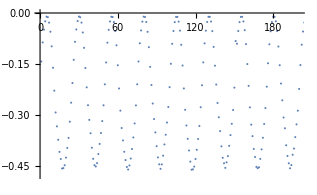

```mathematica
ListPlot[rawRotationData[[1]],PlotRange->{{0,200},Full}]
```